## Number1

#### A)

```mathematica
A=({{.9, .02, .08}, {.05, .85, .1}, {.05, .05, .9}})
```

{{0.9,0.02,0.08},{0.05,0.85,0.1},{0.05,0.05,0.9}}

```mathematica
Solve[{.1x==.05y+.05z&&.15y== .02x+.05z&& .1z== .08x+.1y&&x+y+z==1},{x,y,z}]
```

Solve::ivar: 0.333333 is not a valid variable.

Solve[{True},{0.333333,0.2,0.466667}]

```mathematica
x=0.3333333333333333;y=0.2;z=0.4666666666666667;
```

x=π_1,y=π_2,z=π_3

#### B)

will be in each state 1 week so it will grow at each rate an amount of time proportional to the steady state.

```mathematica
10000(1.03*x+1.28*y+1.1*z)^10
```

29083.8

#### C)

```mathematica
A=({{.9+a, .02 +a, .08-2a}, {.05, .85, .1}, {.05, .05, .9}})
```

{{0.9+a,0.02+a,0.08-2 a},{0.05,0.85,0.1},{0.05,0.05,0.9}}

It wouldn’t solve for a general a so I’ll enter test cases
a=+.01

```mathematica
Solve[{(.09)*xc==.05yc+.05zc&&.15yc== (.03 )*xc+.05zc&& .1zc== (.06)xc+.1yc&&xc+yc+zc==1},{xc,yc,zc}]
```

{{xc→0.357143,yc→0.214286,zc→0.428571}}

```mathematica
10000*(1.03*0.35714285714285715+1.28*0.2142857142857143+1.1*0.4285714285714286)^10
```

29321.1

about 230 bucks more.

a = - .01

```mathematica
Solve[{(.11)*xc==.05yc+.05zc&&.15yc== (.01 )*xc+.05zc&& .1zc== (.1)xc+.1yc&&xc+yc+zc==1},{xc,yc,zc}]
```

{{xc→0.3125,yc→0.1875,zc→0.5}}

```mathematica
10000*(1.03*0.3125+1.28*0.1875+1.1*.5)^10
```

28877.5

about 210 bucks fewer

#### D)

Assuming by order you mean which is labelled π_1,π_2 and π_3 it should not matter as long as the payout maintains relativity.  All operations are equivalenbt regardless of order
(System of equations will not be affected with arbitray variable names and weighted sums will not be affected either given respective integrity is maintained.  Sums are commutative)

## Number 2

#### A)

OverHat[driveTime](minutes)=0.510563+1.402448 OverHat[distance](miles)

#### B)

OverHat[totalTime] (minutes)= 3.2 +OverHat[driveTime](minutes)

OverHat[totalTime] (minutes)= 3.75106+1.402448(miles)

#### C)

```mathematica
f[c_,b_]:=(2.62-(b+1.22*c))^2+(8.35-(b+3.48*c))^2+(6.44-(b+5.1*c))^2+(3.51-(b+3.39*c))^2+(6.52-(b+4.13*c))^2+(2.46-(b+1.75*c))^2+(5.02-(b+2.95*c))^2+(1.73-(b+1.3*c))^2+(1.14-(b+.76*c))^2+(4.56-(b+2.52*c))^2+(2.9-(b+1.66*c))^2+(3.19-(b+1.84*c))^2+(4.26-(b+3.19*c))^2+(7-(b+4.11*c))^2+(5.49-(b+3.09*c))^2+(7.64-(b+4.96*c))^2+(3.09-(b+1.64*c))^2+(3.88-(b+3.23*c))^2+(5.49-(b+3.07*c))^2+(7.64-(b+4.26*c))^2+(3.09-(b+1.64*c))^2+(3.88-(b+3.23*c))^2+(5.49-(b+3.07*c))^2+(6.82-(b+4.26*c))^2+(5.53-(b+4.4*c))^2+(4.3-(b+2.42*c))^2+(3.55-(b+2.96*c))^2//Simplify
```

```mathematica
f[c,b]
```

27. (25.1672+b^2-31.2075 c+10.047 c^2+b (-9.30296+5.89852 c))

```mathematica
f2[c_,b_]:=Expand[27. (25.16715185185185+b^2-31.207496296296295 c+10.046959259259259 c^2+b (-9.302962962962964+5.898518518518518 c))]
```

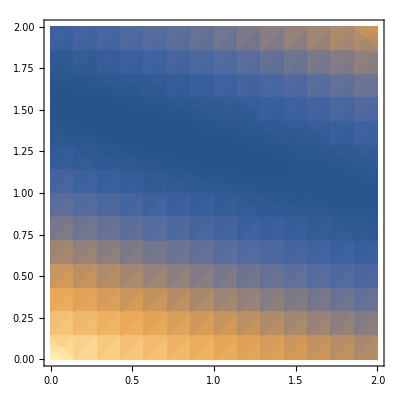

```mathematica
DensityPlot[679.5131-251.18 b+27. b^2-842.6024 c+159.26 b c+271.2679 c^2,{b,0,2},{c,0,2}]
```

```mathematica
Solve[D[f2[c,b],c]==0]
```

{{c→1.55308-0.293547 b}}

```mathematica
Solve[D[f2[c,b],b]==0]
```

{{c→1.57717-0.339068 b}}

```mathematica
Solve[1.5771694085143793-0.3390681903805099 b==1.5530816583901008-0.29354744885038003 b,b]
```

{{b→0.52916}}

c

```mathematica
1.5771694085143793-0.3390681903805099*0.529159879971088
```

1.39775

```mathematica
f[t_]:=0.529159879971088 +1.3977481255906146*t
```

```mathematica
f[5.1]
```

7.65768

```mathematica
The results seem reasonable but the values obviously don't line up with Excels regression.
```